```mathematica
Clear[torsionConstant]
torsionConstant[region:_?RegionQ]:=Module[
{ψ,u,y,z},
ψ=NDSolveValue[{
Laplacian[u[y,z],{y,z}]==-2,
DirichletCondition[u[y,z]==0,True]
},u,{y,z}∈Ω]//Quiet;
2NIntegrate[ψ[y,z],{y,z}∈Ω]
]
```

```mathematica
Clear[crossSection]
crossSection[region:_?RegionQ,units_:"mm"]:=Module[
{data,yt,zt,y,z,colors,w,h},
data={{"Measure","Value","Units"}};

(* Area *)
AppendTo[data,{"A",Area[region],units^2}];

(* Mass center *)
{yt,zt}=NIntegrate[{y,z},{y,z}∈region]/Area[region]//Quiet;

(* Bounds *)
{w,h}=(#[[2]]-#[[1]])&/@RegionBounds[region];

(* Moment of inertia *)
AppendTo[data,{"I_y_t",NIntegrate[(y-yt)^2,{y,z}∈region],units^4}];
AppendTo[data,{"I_z_t",NIntegrate[(z-zt)^2,{y,z}∈region],units^4}];
AppendTo[data,{"I_y_t",NIntegrate[(y-yt)(z-zt),{y,z}∈region],units^4}];
AppendTo[data,{"I_x_t",NIntegrate[(y-yt)^2+(z-zt)^2,{y,z}∈region],units^4}];
AppendTo[data,{"J_t",torsionConstant[region],units^4}];

(* Visualize *)
colors=ColorData[97,"ColorList"];
Grid[{{
Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{RGBColor["#bfbfbf"],None},{RGBColor["#f2f2f2"],None}}],
Show[
RegionPlot[region,AxesLabel->{"y","z"}],
Graphics[{
{Arrow[{{yt-(w+h)/10,zt},{yt+(w+h)/10,zt}}]},
{Arrow[{{yt,zt-(w+h)/10},{yt,zt+(w+h)/10}}]},
{Text[Style["y_t",FontSize->14],{yt+(w+h)/7.7,zt}]},
{Text[Style["z_t",FontSize->14],{yt,zt+(w+h)/7.7}]},
{PointSize[0.03],Point[{yt,zt}]}
}]
]
}}]
]
```

```mathematica
Ω=Disk[{0,0},1];
```

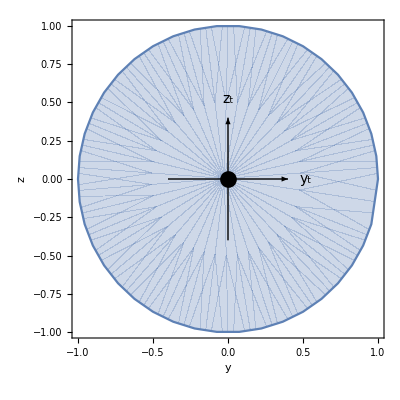
Measure | Value | Units
A | π | mm^2
I_y_t | 0.785398 | mm^4
I_z_t | 0.785398 | mm^4
I_y_t | 0. | mm^4
I_x_t | 1.5708 | mm^4
J_t | 1.57081 | mm^4 | -Graphics-

```mathematica
crossSection[Ω]
```